```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Variables to change *)
pictureName="Capture.png";
fiberDiameter=200; (* υm *)
framesToExportEvery=5;
```

```mathematica
(* Main script NOT to change *)
```

```mathematica
DeleteFile[FileNames[NotebookDirectory[]<>"//Result//"<>"*.*"]];
```

```mathematica
(* Part I *)
```

```mathematica
img0=Import[NotebookDirectory[]<>pictureName];
img1=Image[ImageData[img0][[;;,;;,1]]];
img2=ColorQuantize[img1,3];
img2=img1;
img3=ColorNegate[img2];
```

```mathematica
data0=ImageData[img3];
data1=data0-Min[data0];
```

```mathematica
dataBottom=Chop[data1[[-1,All]]];
nonzeroPositions=Position[dataBottom,_?(#≠0 &)];
firstNonzero=nonzeroPositions[[1,1]];
lastNonzero=nonzeroPositions[[-1,1]];
fiberLengthPixels=lastNonzero-firstNonzero;
fiberLengthReal=fiberDiameter;
umInPixel=N[fiberLengthReal/fiberLengthPixels];
```

```mathematica
data2=data1;
For[row=1,row<Dimensions[data1][[1]],row++,
whiteColor=0.4;
whitePositions=Position[data2[[row,All]],_?(#>whiteColor&)];
If[Length[whitePositions]>0,
firstWhite=whitePositions[[1,1]];
lastWhite=whitePositions[[-1,1]];
For[column=firstWhite,column<lastWhite,column++,
data2[[row,column]]=0×whiteColor]
,Indeterminate
];
];
```

```mathematica
img4=Image[data2];
```

```mathematica
Show[img4,ImageSize->Medium];
```

```mathematica
img=ColorNegate[Image[ImageData[img4][[;;-5,All]]]];
```

```mathematica
(* Part II *)
```

```mathematica
bin=Thinning@ColorNegate[Binarize[img]];
```

```mathematica
pts=N[PixelValuePositions[bin,1.]];
```

```mathematica
dist=Outer[EuclideanDistance,pts,pts,1];
g=WeightedAdjacencyGraph[dist,DirectedEdges->False];
```

```mathematica
st=FindSpanningTree[g];
```

```mathematica
endVertices=Position[VertexDegree[st],1][[All,1]];
HighlightImage[bin,pts[[endVertices]]];
```

```mathematica
allPaths=Flatten[Outer[FindShortestPath[st,#1,#2]&,endVertices,endVertices],1];

longestPath=MaximalBy[allPaths,Length][[1]];

Graphics[{Red,Line[pts[[longestPath]]]}];
```

```mathematica
curve=pts[[longestPath]];

σ=35;

{{dx1,dy1},{dx2,dy2}}=Table[GaussianFilter[curve[[All,dim]],σ,der],{der,2},{dim,2}];

κ=(dx1*dy2-dx2*dy1)/((dx1^2+dy1^2)^(3/2));
```

```mathematica
κ=Chop[κ];
nonzeroPositions=Position[κ,_?(#≠0 &)];
firstNonzero=nonzeroPositions[[1,1]];
lastNonzero=nonzeroPositions[[-1,1]];
κ=κ[[firstNonzero;;lastNonzero]];
```

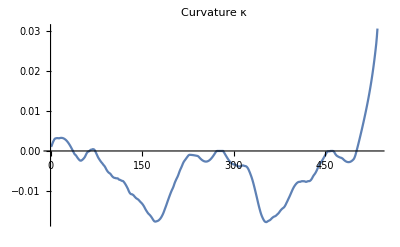

```mathematica
ListLinePlot[κ,PlotRange->All,PlotLabel->"Curvature κ"]
```

```mathematica
Off[Power::infy]
Off[Clip::nord]
Off[Part::partw]
Monitor[
picTable=Table[
rout=Clip[1/κ[[i]],{-1,1}*10^6];
pic=Show[
ListLinePlot[curve,
PlotLabel->"Curvature r = "<>ToString[rout×umInPixel]<>" υm",
Epilog->Module[
{r,pt,n},
(pt=curve[[i]];
r=rout;
n=Normalize[{dy1[[i]],-dx1[[i]]}];
{Red,
PointSize[Large],
Point[pt],
Circle[pt-n*r,Abs[r]]}
)
]
],
img3,
ListLinePlot[curve]
];
Export[NotebookDirectory[]<>"//Result//"<>ToString[i]<>".png",pic]
,{i,1,Length[curve],framesToExportEvery}];
,ToString[i]<>" of "<>ToString[Length[curve]]];
```